```mathematica
ClearAll[polyhedronfacegraph];

polyhedronfacegraph[polyhedron_]:= 

    Block[{dualpolyhedron, vertexlist, vertexpairings, sortedvertices},

    dualpolyhedron = DualPolyhedron[polyhedron];  
    vertexlist = dualpolyhedron[[2]];   

    vertexpairings = Flatten[Table[Append[

       Partition[vertexlist[[n]], 2, 1], 
       {Last[vertexlist[[n]]], First[vertexlist[[n]]]}],  
       {n, 1, Length[vertexlist]}], 1];

    sortedvertices = Sort /@ vertexpairings // DeleteDuplicates; 

    Graph[UndirectedEdge@@@sortedvertices,VertexLabels -> "Name"] 
]

ClearAll[generatetrees];

generatetrees[graph_] := Table[FindSpanningTree[{graph, n}], {n, 1, VertexCount[graph]}]

ClearAll[normvector];

normvector[coords_] := Cross[coords[[2]] - coords[[1]], coords[[3]] - coords[[1]]];

ClearAll[generatenetcoords];

generatenetcoords[mesh_, tree_]:=

    Block[{transformations, transformedmesh, meshlist, transformedmeshlist, normals, polygonfaces, transformedrotation},

       polygonfaces = Reap[

         meshlist = MeshPrimitives[mesh, 2][[All, 1]];

         transformations =      
			RotationTransform[{normvector[meshlist[[1]]], {0, 0, -1}}] @* 
				TranslationTransform[-PropertyValue[{mesh, {2, 1}}, MeshCellCentroid]];  

         transformedmesh = TransformedRegion[mesh, transformations];      
         transformedmeshlist = MeshPrimitives[transformedmesh, 2][[All, 1]];     

         normals = normvector[#] &/@ transformedmeshlist;    

         Sow[transformedmeshlist[[1]], "flat"];

         transformedrotation[1] = TransformationFunction[IdentityMatrix[4]];

         BreadthFirstScan[tree, 1, "DiscoverVertex" -> unfold[transformedmeshlist, normals, transformedrotation]];,  
         {"flat"}][[-1, All, 1]];
       Chop[polygonfaces]
		]

ClearAll[unfold];

unfold[meshlist_, normals_, transformedrotation_][u_, v_, _] /; (u =!= v) :=

	Block[{edgecoord1, edgecoord2, angle, rotation},
	
		{edgecoord1, edgecoord2} = Intersection @@ meshlist⟦{u, v}⟧; 
		angle = DihedralAngle[{edgecoord1, edgecoord2}, normals⟦{u, v}⟧];
		rotation = RotationTransform[angle, edgecoord2 - edgecoord1, Mean[{edgecoord1, edgecoord2}]];
		transformedrotation[u] = transformedrotation[v]@*rotation;
		Sow[transformedrotation[u] @ meshlist⟦u⟧, "flat"];
	]
	
testforoverlap[polyhedron_, netcoords_] := 

		Block[{surfacearea, netsurfacearea},
		
            surfacearea = SurfaceArea[polyhedron];
            netsurfacearea = RegionMeasure[RegionUnion[Polygon /@ netcoords]];
            Return[surfacearea == netsurfacearea];
            
        ]
       
ClearAll[generateallnets];

generateallnets[polyhedron_] := 

    Block[{netcoords, trees, graph, mesh, surfacearea, netsurfacearea, goodnets},

    mesh = BoundaryDiscretizeGraphics[polyhedron];   
    graph = polyhedronfacegraph[polyhedron];
    trees = generatetrees[graph];

    goodnets = {};   

    Table[     
    
        netcoords = First@generatenetcoords[mesh, trees[[treeposition]]];    
        netcoords = Table[Delete[netcoords[[n, m]], {3}], {n, 1, Length[netcoords]}, {m, 1, 3}];        
		
        If[testforoverlap[polyhedron, netcoords] == True,             
           AppendTo[goodnets, Graphics[{Hue[0.94, 0.22, 1.], EdgeForm[{Thin, Pink}], Polygon /@ netcoords}]]        
        ];,  

        {treeposition, 1, Length[trees]} 
    ];    

    Row[{Graphics3D[polyhedron], goodnets}]
]

ClearAll[generatefastnet];

generatefastnet[polyhedron_] := 
Block[{netcoords, trees, graph, mesh, surfacearea, netsurfacearea, goodnets},

mesh = BoundaryDiscretizeGraphics[polyhedron]; 
graph = polyhedronfacegraph[polyhedron];
trees = generatetrees[graph];

netcoords = First@generatenetcoords[mesh, trees[[1]]];
netcoords = Table[Delete[netcoords[[n, m]], {3}], {n, 1, Length[netcoords]}, {m, 1, 3}];

Print[Graphics[{Hue[0.9,0.18,1.], EdgeForm[{Thin, Hue[0.9,0.98,1.]}], Polygon /@ netcoords}]]]
```

-Graphics3D-

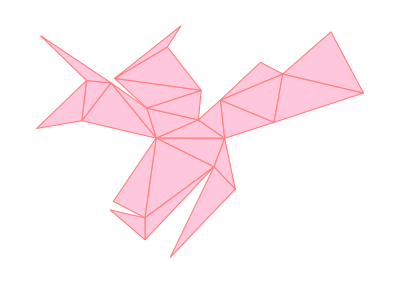
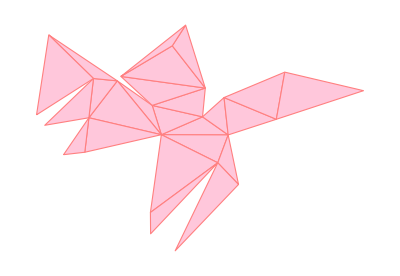
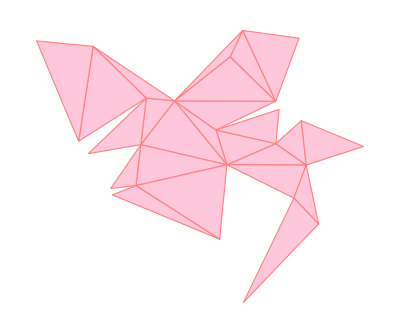
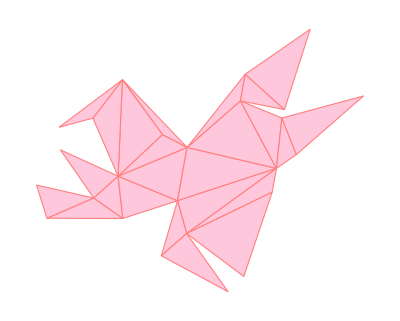
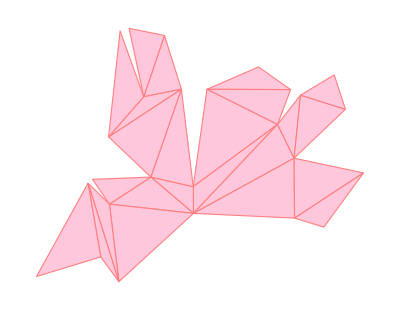
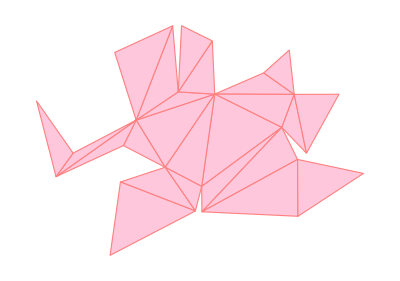
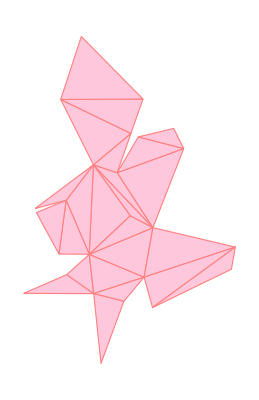
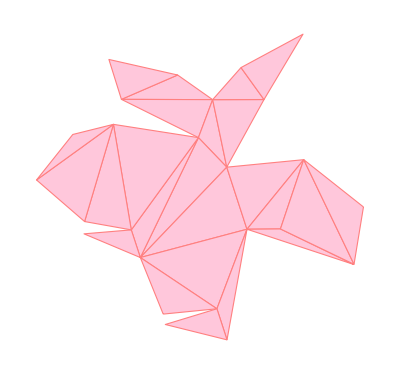
-Graphics3D-{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sunny = RandomPolyhedron[{"ConvexHull",20}];
Graphics3D[sunny]
generateallnets[sunny]
```